# e.Numeric.series-full.rencon2.strange.L-0.90.ci-1.5.mass-limit.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.formfactors\e.Numeric.series-full.rencon2.strange.L-1.00.ci-1.5.mass-limit.nb

## note

use full integral analytic expression to draw pictures.

s flavor in proton has no contribution, so  the rencon is zero.

for perspective quark, use perspective fucoeandmrrlnm

this nb is to numeric evaluating the Γμs

and draw pictures.

if consider 1/((1+Q^2/Λ^2)^2)→c^2/((1+Q^2/Λ^2)^2) ,c^2=((Λ^2+mπ^2)/Λ^2)^2,then c^2={1.05349 mπ, 1.79549 mKi, 2.0984 mη}

for different particles, use different rencon

## Initial

inital by hand

```mathematica
<<X`
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
choplimit=10^-8;
```

## coefficients & mass constants

a 4 component list, contain all, u,d,s

coe list and mass rule list initial

```mathematica
Once[fucoe=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

```mathematica
Once[fumass=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

coe list and mass rule get

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"analytic-storage.strange.series-full"}]]
```

C:\Users\Tom\Desktop\octet.formfactors\analytic-storage.strange.series-full

```mathematica
zero`directory=FileNameJoin[{NotebookDirectory[],"analytic-storage.strange.series-o0"}]
```

C:\Users\Tom\Desktop\octet.formfactors\analytic-storage.strange.series-o0

```mathematica
coe`directory=FileNameJoin[{NotebookDirectory[],"expression-coes"}]
```

C:\Users\Tom\Desktop\octet.formfactors\expression-coes

```mathematica
fucoeandmrrlnm={
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.all.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.u.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.d.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.s.m"}]
};
```

```mathematica
Once[chpt`qfb`quench`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfb`quench`coemass`masslimit.m"}]]];
Once[chpt`qfa`sea`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfa`sea`coemass`masslimit.m"}]]];
Once[chpt`qfa`valence`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfa`valence`coemass`masslimit.m"}]]];
```

```mathematica
Once[
fucoeandmrrlraw=Map[Get,fucoeandmrrlnm,1]
];
```

```mathematica
Once[
fucoeandmrrl=Join[fucoeandmrrlraw,
Transpose[chpt`qfb`quench`coemass`masslimit,{2,3,1}],
Transpose[chpt`qfa`valence`coemass`masslimit,{2,3,1}],
Transpose[chpt`qfa`sea`coemass`masslimit,{2,3,1}]
]
];
```

```mathematica
fucoeandmrrlraw//Dimensions
fucoeandmrrl//Dimensions
```

{4,11,8}

{13,11,8}

mass constant

## order

conmo={1Σ,2Neu,3Ξ,4Λ}--{1Σm,2Σ0,3Σp,4pr,5ne,6Ξm,7Ξ0,8Λ}

conmm={1π,2Ki,3η},

conmd={1Δ,2Σs,3Ξs,4Ω}

## assign value

```mathematica
Once[
{conmπ,conmKi,conmη,conmEtas}={
0.1381,
0.4956,
0.5693,
0.9452
}
];
```

```mathematica
Once[
{conmΣ,conmN,conmΞ,conmΛ,conmΛΣ,
conmUUU,conmDDD,conmSSS(* the symmetric terms *)
}={
1.193,0.939,1.315,1.116,1.155,
0.939,0.939,1.315
}
];
```

```mathematica
{conmΔ,conmΣs,conmΞs,conmΩ}={
1.232,
1.385,
1.530,
1.672
};
```

```mathematica
{conmN,conmη,conmΞs}
```

{0.939,0.5693,1.53}

fu Coefficients mass rules reduce

## fu Coefficients

in {4,9} external sign[-]

fusign8,fusign9

```mathematica
fucoepresign={
(*+++++++++++++++++++111++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,fusign8,(*8*)fusign9,(*9*)
1,1(*11*)},
(*+++++++++++++++++++222++++++++++++++++++++++++++++++++++++++*)
{
-1,-1,-1,
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)},
(*+++++++++++++++++++333++++++++++++++++++++++++++++++++++++++*)
{1,1,1,(*3*)
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)1,(*9*)
1,1(*11*)}(*fch's sign*)
}⟦3⟧;
```

1 for fitting, 2 for calc/test,

```mathematica
(*fucoeandmrrlraw [consti,figure,octet][4*11*8]*)
fucoe=Table[
Simplify[
fucoepresign*Values[fucoeandmrrl⟦i⟧]
]
,{i,1,13,1}
];//AbsoluteTiming
```

{2.04873,Null}

## fu mass rules

```mathematica
fumass=Keys[fucoeandmrrl];
```

```mathematica
fucoe//Dimensions
fumass//Dimensions
```

{13,11,8}

{13,11,8}

magnetic momentum tree level

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};

rule lists

```mathematica
constmo={
(*1*)conmΣ,(*2*)conmΣ,(*3*)conmΣ,
(*4*)conmN,(*5*)conmN,
(*6*)conmΞ,(*7*)conmΞ,
(*8*)conmΛ
};
```

```mathematica
baselist1={
{mN->conmΣ},{mN->conmΣ},{mN->conmΣ},
{mN->conmN},{mN->conmN},
{mN->conmΞ},{mN->conmΞ},
{mN->conmΛ}
};
```

c1→2.081,c2→(2/3 c1-1),c3→(-1/3 c1-1)

```mathematica
c3 = c2 - c1;
```

```mathematica
baselist2={
f->0.093,
zi->-1,
di->0.76,fi->0.50,
ci->1.5,Λ0->1,
c1->0.9172210785221936,c2->0.5396939118971014
};
```

for neutron pull-apart, best octet fit Λ0≈1~0.1

```mathematica
baselist=Table[
Join[baselist1⟦i⟧,baselist2]
,{i,1,8,1}
];
```

## para-c1c2.sum-square.all-baryons.rencon2

*********************************************************************

ci→1,Λ0→0.7,
{0.140654,{c1→2.01272,c2→0.477586}}

ci→1,Λ0→0.75,
{0.132188,{c1→1.95069,c2→0.441996}}

ci→1,Λ0→0.8,
{0.126797,{c1→1.88383,c2→0.405126}}

ci→1,Λ0→0.85,
{0.123918,{c1→1.81213,c2→0.36732}}

ci→1,Λ0→0.90,
{0.123053,{c1→1.73562,c2→0.329194}}

ci→1,Λ0→0.95,
{0.123788,{c1→1.65425,c2→0.291768}}

ci→1,Λ0→1.0,
{0.125804,{c1→1.56783,c2→0.256696}}

ci→1,Λ0→1.05,
{0.128887,{c1→1.4758,c2→0.226666}}

ci→1,Λ0→1.1,
{0.132961,{c1→1.37675,c2→0.206175}}

**********************************************************************************

ci→1,Λ0→0.90,
{0.123053,{c1→1.73562,c2→0.329194}}

Λ0→0.90,ci→1.05,
{0.114994,{c1→1.69533,c2→0.331066}}

Λ0→0.90,ci→1.1,
{0.107251,{c1→1.65427,c2→0.334366}}

Λ0→0.90,ci→1.15,
{0.099849,{c1→1.61237,c2→0.339155}}

Λ0→0.90,ci→1.2,

{0.0928122,{c1→1.56956,c2→0.345494}}

Λ0→0.90,ci→1.25,
{0.0861669,{c1→1.52573,c2→0.353452}}

Λ0→0.90,ci→1.3,
{0.0799395,{c1→1.48082,c2→0.363103}}

Λ0→0.90,ci→1.35,

{0.0741573,{c1→1.43471,c2→0.374525}}

Λ0→0.90,ci→1.40,
{0.0688482,{c1→1.38729,c2→0.387806}}

Λ0→0.90,ci→1.45,
{0.0640414,{c1→1.33846,c2→0.403039}}

Λ0→0.90,ci→1.5,
{0.0597673,{c1→1.28808,c2→0.420326}}

*************************************************************************

Λ0→0.80,ci→1,
{0.126797,{c1→1.88383,c2→0.405126}}

Λ0→0.80,ci→1.05,
{0.119196,{c1→1.85488,c2→0.403562}}

Λ0→0.80,ci→1.1,
{0.111782,{c1→1.82541,c2→0.402675}}

Λ0→0.80,ci→1.15,
{0.104581,{c1→1.79539,c2→0.402487}}

Λ0→0.80,ci→1.2,

{0.097619,{c1→1.7648,c2→0.403024}}

Λ0→0.80,ci→1.25,
{0.0909201,{c1→1.73361,c2→0.40431}}

Λ0→0.80,ci→1.3,
{0.0845108,{c1→1.70178,c2→0.406373}}

Λ0→0.80,ci→1.35,

{0.0784171,{c1→1.6693,c2→0.409241}}

Λ0→0.80,ci→1.40,
{0.0726658,{c1→1.63611,c2→0.412944}}

Λ0→0.80,ci→1.45,
{0.0672835,{c1→1.60219,c2→0.417514}}

Λ0→0.80,ci→1.5,
{0.0622978,{c1→1.56749,c2→0.422984}}

************************************************************

Λ0→0.85,ci→1.5,
{0.0597742,{c1→1.43562,c2→0.412794}}

Λ0→1,ci→1.5,
{0.0654518,{c1→0.917221,c2→0.539694}}

## para test c1c2 sum - square

fch,ci→1,Λ0→0.9,
c1→2.081,c2→0.788,c3→-1.693
{0.0434328,{c1→2.00193}}

ci→1,Λ0→0.8,
 {4.55972×10^-17,{c1→2.14188,c2→0.756261}}

ci→1,Λ0→0.85,
 {6.40949×10^-31,{c1→2.09749,c2→0.752286}}

ci→1,Λ0→0.90,
 {1.33761×10^-17,{c1→2.05739,c2→0.747545}}

ci→1,Λ0→0.95
 {3.9443×10^-31,{c1→2.02149,c2→0.741624}}

ci→1,Λ0→1.0,
 {1.32802×10^-16,{c1→1.98969,c2→0.734099}}

## Γμ get

pure diagram form-factor

```mathematica
Clear[ff1,ff2]
```

```mathematica
Once[Monitor[
ff1=Table[
Get[
FileNameJoin[{Directory[],"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
ff2=Table[
Get[
FileNameJoin[{Directory[],"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{28.8231,Null}

```mathematica
Once[Monitor[
zero`ff1=Table[
Get[
FileNameJoin[{zero`directory,"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
zero`ff2=Table[
Get[
FileNameJoin[{zero`directory,"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{0.204278,Null}

```mathematica
ff1//Dimensions
zero`ff2//Dimensions
```

form-factor f1, f2

## form-factor list

fucoe=11[diagram]*8[octet]*n(a coefficients lists of n elements)

fumass=11[diagram]*8[octet]*n(n ==above n,n mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
fucoe⟦2,4⟧
```

```mathematica
Length[fucoe⟦2,4⟧]
```

contribution combine coefficients,f1, f2

```mathematica
SetOptions[Simplify,TimeConstraint->1];
```

fucoe=11[diagram]*8[octet]*n(coefficients)

fumass=11[diagram]*8[octet]*n(n =above n,mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
Once[nuff1=Table[0,{seva,1,13,1},{io,1,8,1}]];
Once[nuff2=Table[0,{seva,1,13,1},{io,1,8,1}]];
```

```mathematica
Monitor[
Table[
(nuff1⟦seva⟧=Total[
Table[
Simplify[
(
(
fucoe⟦seva,diag,oct,coe⟧*ff1⟦diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦seva,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦seva,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
(nuff2⟦seva⟧=Total[
Table[
Simplify[
(
(
fucoe⟦seva,diag,oct,coe⟧*ff2⟦diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦seva,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦seva,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
,{seva,{1}}
];
,{seva,oct,diag,coe}
]//AbsoluteTiming
```

{645.389,Null}

```mathematica
(*nuff1,nuff2 is 4*8*)
nugegm=Transpose[(*8*4*2 transpose into 4*8*2*)
Table[
-1/(16 π^2){
nuff1⟦;;,i⟧-Q2/(4 constmo⟦i⟧^2)nuff2⟦;;,i⟧,
nuff1⟦;;,i⟧+nuff2⟦;;,i⟧
}
,{i,1,8,1}]
,{2,3,1}
];//AbsoluteTiming
```

{0.0042538,Null}

```mathematica
nuff1//Dimensions
nuff2//Dimensions
nugegm//Dimensions
```

{13,8}

{13,8}

{13,8,2}

## zero`nuff1 zero`nuff2

```mathematica
zero`nuff1=Table[0,{consti,1,13,1}];
zero`nuff2=Table[0,{consti,1,13,1}];
```

```mathematica
Monitor[
Table[
(
zero`nuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*zero`ff1⟦diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
(
zero`nuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*zero`ff2⟦diag⟧
)/.baselist⟦oct⟧/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]
);
,{constituent,1,13,1}
];
,{constituent,oct,diag,coe}
]//AbsoluteTiming
(*nuff1,nuff2 is 4*8*)
```

{74.4171,Null}

```mathematica
zero`nugegm=Transpose[(*8*4*2 transpose into 4*8*2*)
Table[
-1/(16 π^2){
zero`nuff1⟦;;,i⟧-Q2/(4 constmo⟦i⟧^2)zero`nuff2⟦;;,i⟧,
zero`nuff1⟦;;,i⟧+zero`nuff2⟦;;,i⟧
}
,{i,1,8,1}]
,{2,3,1}
];//AbsoluteTiming
```

{0.0050509,Null}

```mathematica
zero`nuff1//Dimensions
zero`nuff2//Dimensions
zero`nugegm//Dimensions
```

{13,8}

{13,8}

{13,8,2}

## tree level contributions

initial

because history reasons, all mass mo here is marked as mN

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(c1 Q2)/(√3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(4 c1 mN^2)/(√3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

```mathematica
trf1f2={
(*+++++++++++++++++total++++++++++++++++++++++++*)
{{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{-(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}},
(*+++++++++++++++++u++++++++++++++++++++++++*)
{
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++d++++++++++++++++++++++++*)
{
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++s++++++++++++++++++++++++*)
{{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+4 c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (4 c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}}
}/.mo->mN;
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

gegm

-I el(4 mN^2+c1 Q2)/(4 mN^2+Q2) ,--el/(2mN)(4 (c1-1) mN^2)/(4 mN^2+Q2)

netrf1f2⟦4⟧={(4 mN^2+c1 Q2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2),(4 (c1-1) mN^2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2)}/.baselist

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

```mathematica
trgegm=Transpose[
Table[
Simplify[
{
trf1f2⟦;;,i,1⟧-Q2/(4 constmo⟦i⟧^2)trf1f2⟦;;,i,2⟧,
trf1f2⟦;;,i,1⟧+trf1f2⟦;;,i,2⟧
}/.baselist⟦i⟧
]
,{i,1,8,1}]
,{2,3,1}];//AbsoluteTiming
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

{0.0129183,Null}

```mathematica
trgegm//Dimensions
```

{4,8,2}

plot

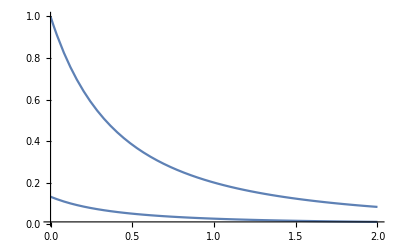

```mathematica
Plot[
trgegm⟦4,1⟧
,{Q2,0.,2.},PlotRange->Full
]
```

```mathematica
Plot[
trgegm⟦4,2⟧
,{Q2,0.,2.},PlotRange->Full
]
```

-Graphics-

```mathematica
Plot[
trgegm⟦5,1⟧
,{Q2,0.,2.},PlotRange->Full]
```

Part::partw: {«1»} 的部分 5 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

-Graphics-

```mathematica
Plot[
trgegm⟦5,2⟧
,{Q2,0.,2.},PlotRange->Full]
```

Part::partw: {«1»} 的部分 5 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

-Graphics-

## loopd0

```mathematica
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"};
```

loop derivative coefficient

to order 0

{loopged0,loopgmd0}

nugegm⟦consti,oct,F1F2⟧4*8*2

```mathematica
{loopged0,loopgmd0}=Transpose[(*[oct,loop,consti]8*6*4 transpose into [loop,consti,oct][6*4*8]*)
Table[
{
zero`nugegm⟦;;,oct,1⟧,
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
zero`nugegm⟦;;,oct,2⟧
}
,{oct,1,8,1}
]
,{3,1,2}];//AbsoluteTiming
(*{loopged0,loopgmd0} ⟦consti,oct⟧[4,8]*)
```

{0.0006254,Null}

```mathematica
loopged0//Dimensions
loopgmd0//Dimensions
```

{13,8}

{13,8}

## rencon calc

constants

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

```mathematica
octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
};
```

```mathematica
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};
```

rencon2.13

```mathematica
rencon=Table[1,{seva,1,13,1},{io,1,8,1}];
(*+++++++++++++++++renormalized according to charge+++++++++++++*)
Table[
rencon⟦;;,i⟧=Abs[octetcharge⟦i⟧-Re[(Cancel[Chop[loopged0⟦1,i⟧,choplimit]]/.Q2->0)]]
,{i,{1,3,4,6}}];
rencon⟦;;,2⟧=rencon⟦;;,3⟧;
rencon⟦;;,5⟧=rencon⟦;;,4⟧;
rencon⟦;;,7⟧=rencon⟦;;,6⟧;
rencon⟦;;,8⟧=Abs[1-Re[(Cancel[Chop[loopged0⟦2,8⟧,choplimit]]/.Q2->0)]];
(*++++++++++++++++++++no renormalized+++++++++++++++++++++*)
(*rencon⟦2,1⟧=1;
rencon⟦2,6⟧=1;
rencon⟦3,3⟧=1;
rencon⟦3,7⟧=1;
rencon⟦4,4⟧=1;
rencon⟦4,5⟧=1;*)
(*++++++++++++++++++++display+++++++++++++++++++++*)
TableForm[rencon,TableHeadings->{Automatic,None}]
```

1 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
2 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
3 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
4 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
5 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
6 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
7 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
8 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
9 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
10 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
11 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
12 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116
13 | 0.313345 | 0.313345 | 0.313345 | 0.228249 | 0.228249 | 0.482083 | 0.482083 | 0.36116

## graphics automatic & optimize

exprimental value

electric magneton:

μB=(e ℏ)/(2me),9.274009994(57)*10^-24 SI

μN=(e ℏ)/(2mN),

ne −1.9130427±0.0000005 μN

pr 2.7928473446±0.0000000008 μN

Λ μ=−0.613±0.004 μN

Σp μ=2.458±0.010 μN

Σ0 μΣΛ=1.61±0.08 μN

Σm μ=−1.160±0.025 μN

Ξ0 μ=−1.250±0.014 μN

Ξm μ=−0.6507±0.0025 μN

```mathematica
octetmageton={
−1.160,(*1Σm*)
0.76,(*2Σ0*)
2.458,(*3Σp*)
2.7928473446,(*4pr*)
−1.9130427,(*1Ne*)
−0.6507,(*6Ξm*)
−1.250,(*7Ξ0*)
−0.613(*8Λ*)
};
```

```mathematica
octetcharge={
-1,(*1*)0,1,1,(*4*)0,-1,(*6*)0,(*7*)0(*8*)};
```

name

```mathematica
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"};
```

```mathematica
octetnameabbr=
{"Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"};
```

```mathematica
diagname={"1a","2b","3c","4de","5fg","6h","7i","8j","9kl","10mn","11op"};
```

```mathematica
fig`geconstiname={"1 ge.all","2 ge.u","3 ge.d","4 ge.s",
"5 ge.u-quench","6 ge.d-quench","7 ge.s-quench",
"8 ge.u-valence","9 ge.d-valence","10 ge.s-valence",
"11 ge.u-sea","12 ge.d-sea","13 ge.s-sea"
};
fig`gmconstiname={"1 gm.all","2 gm.u","3 gm.d","4 gm.s",
"5 gm.u-quench","6 gm.d-quench","7 gm.s-quench",
"8 gm.u-valence","9 gm.d-valence","10 gm.s-valence",
"11 gm.u-sea","12 gm.d-sea","13 gm.s-sea"
};
```

```mathematica
Once[
expfit`gegm=Table[0,{consti,1,13,1},{octet,1,8,1},{gegm,1,2,1}];
expfit`gegm⟦1,4,1⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->-0.24,b1->10.98,b2->12.82,b3->21.97,zero`value->1,mp->0.9383};

expfit`gegm⟦1,4,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->0.12,b1->10.97,b2->18.86,b3->6.55,zero`value->2.79,mp->0.9383};
expfit`gegm⟦1,5,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->2.33,b1->14.72,b2->24.2,b3->84.1,zero`value->-1.93,mp->0.9396};
expfit`gegm⟦1,5,1⟧=(fit`A Q2/(4 mp^2))/(1+fit`B Q2/(4 mp^2))Λ2^2/(Q2+Λ2)^2/.{fit`A->1.70,fit`B->3.30,Λ2->0.71,mp->0.9396};
]
```

fun`graph`octet

```mathematica
fig`cutlimit=0.00001;
fig`leadersize=4;
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

figure`ge

## ge`total

```mathematica
fig`calc`baryons`ge`total=Table[0,{io,1,8,1}];
consit=1;(*io=5;*)gegm=1;
Monitor[
Table[
(fig`calc`baryons`ge`total⟦io⟧=(Plot[
#1,
{Q2,0,1},
AxesOrigin->{0,0},
PlotRange->{{0,1},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
]&/@
(*=====================================================*)
{
rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧,(*"Tree"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{loopged0⟦consit,io⟧,Q2≤fig`cutlimit},
{Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
],
(*"Loop"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{rencon⟦consit,io⟧*(trgegm⟦consit,io,gegm⟧/.Q2->0)+loopged0⟦consit,io⟧,Q2≤fig`cutlimit},
{rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧+Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
(*"Total"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
}
)
)
,{io,1,8,1}
]
,io
];
```

## ge`u

1Total, 2u,3d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

```mathematica
consit=11;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`u=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.u","Subsection"],{{Top,Left}}
]
```

## ge`d

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

```mathematica
consit=12;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`d=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.d","Subsection"],{{Top,Left}}
]
```

## ge`s

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u,d,13s

```mathematica
consit=13;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`s=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.s","Subsection"],{{Top,Left}}
]
```

figure`gm

## gm`total

```mathematica
fig`calc`baryons`gm`total=Table[0,{io,1,8,1}];
consit=1;(*io=5;*)gegm=2;
Monitor[
Table[
te`zero`gm=rencon⟦consit,io⟧*(trgegm⟦consit,io,gegm⟧/.Q2->0)+loopgmd0⟦consit,io⟧;
(fig`calc`baryons`gm`total⟦io⟧=(Plot[
#1,
{Q2,0,1},
AxesOrigin->{0,0},
PlotRange->{{0,1},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
]&/@
(*=====================================================*)
{
Abs[rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧/te`zero`gm],(*"Tree"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{Abs[loopgmd0⟦consit,io⟧/te`zero`gm],Q2≤fig`cutlimit},
{Abs[Re[nugegm⟦consit,io,gegm⟧]/te`zero`gm],Q2>fig`cutlimit}
}
],
(*"Loop"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{Abs[(rencon⟦consit,io⟧*(trgegm⟦consit,io,gegm⟧/.Q2->0)+loopgmd0⟦consit,io⟧)/te`zero`gm],Q2≤fig`cutlimit},
{Abs[(rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧+Re[nugegm⟦consit,io,gegm⟧])/te`zero`gm],Q2>fig`cutlimit}
}
]
(*"Total"*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++*)
}
)
)
,{io,1,8,1}
]
,io
];
```

## gm`u

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u10,d,13s

```mathematica
consit=11;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`u=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
AxesOrigin->{0,0},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.u","Subsection"],{{Top,Left}}
]
```

## gm`d

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

```mathematica
consit=12;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`d=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.d","Subsection"],{{Top,Left}}
]
```

## gm`s

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u,d,13s

```mathematica
consit=13;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`s=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
PlotStyle->{Directive[Dashed,AbsoluteThickness[0.7]]},
AxesOrigin->{0,0},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.s","Subsection"],{{Top,Left}}
]
```

storage

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"expression-fig"}]
```

C:\Users\Tom\Desktop\octet.formfactors\expression-fig

## ge

```mathematica
Export[
FileNameJoin[{directory`fig,"fig.calc.baryons.ge.tot.L-1.00.ci-1.5.m"}]
,fig`calc`baryons`ge`total
];
(*Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.d.L-0.90.m"}],fig`calc`nucleon`ge`d];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.s.L-0.90.m"}],fig`calc`nucleon`ge`s];*)
```

## gm

```mathematica
Export[
FileNameJoin[{directory`fig,"fig.calc.baryons.gm.tot.L-1.00.ci-1.5.m"}]
,fig`calc`baryons`gm`total
];
(*Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.d.L-0.90.m"}],fig`calc`nucleon`gm`d];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.s.L-0.90.m"}],fig`calc`nucleon`gm`s];*)
```